# Homework assignment 5

This notebook contains problem descriptions and code needed for assignment #5, Caltech BE/CS 191a, Winter 2026.   Prof. Erik Winfree <winfree@caltech.edu>
Do not share this with anyone who is not currently taking the class.

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"DeterministicCRNsInBulk.nb"}],EvaluationElements->"InitializationCell"]
(* the next line ensures that the command-. keystroke will still (usually) abort an ongoing calculation, fixing a front-end bug *)
MathLink`LinkAddInterruptMessageHandler[$ParentLink];
```

## Required prelude: Further thoughts about Homework 3 and/or Homework 4

As before, please write a paragraph each assessing your thoughts about prior homework.  Review the comments from the graders of your homework, if they’ve been posted.  This assignment is intended to be just one paragraph of worth-reading thoughts about each of the prior homework, not coding or further technical exploration.  Although, of course you are as usual free to pursue the spirit of this exercise in any way you deem to be meaningful and worthwhile engagement.

## Part 1: Chemical computation of algebraic expressions (30 points)

The goals of this homework are for you to:

(1) Get familiar with the CRN simulator package and the examples in DeterministicCRNsInBulk.nb.
(2) Use the modules discussed in class for analog catalytic steady-state computation to build circuits.
(3) Think about the difference between systematically generated circuits and hand-optimized ones.

So, your first task is to choose an analog function of interest, where “interest” means that it is insightful to consider for the purpose of this homework, and/or you like it.  Don’t choose something so trivial such that it makes this homework dumb.  Don’t choose something so complex that doing this homework becomes tedious.  If your function is an algebraic expression, great!  If not, reconsider whether you want to instead choose an algebraic expression.  If not, then consider and explain a suitable approximation, as necessary.  Discuss issues regarding input variables being positive and subexpressions remaining positive.

Example:  You might choose an algebraic expression that represents a solution to the quadratic formula, or a pair of expressions that represent both possible solutions.   A natural choice would be for the input variables would be positive coefficients  a, b, and c  for the quadratic polynomial a x^2-b x +c=0 ,  and the output variables would be 

	[x_1]=([b]+√([b]^2- 4 [a] [c]))/(2 [a])
and
	[x_2]=([b]-√([b]^2- 4 [a] [c]))/(2 [a])

at least for inputs where these values are positive with no imaginary part.   Under certain circumstances, we would get negative subexpressions, so thinking about when that happens, depending on where you put your parentheses, would be part of the problem.

You many analyze this example if you wish, but maybe it’s a little complex and you can choose another interesting algebraic expression that’s just as insightful to consider.

Your second task is to convert your analog function to a CRN using the “plug-and-play” circuit of modular approach described in class, and discuss any issues that arise there for your specific function.  Example issues to consider: When will it be guaranteed to go to steady state?  Are there any “hidden” intermediate species that might go to infinity?  For what input variable values is it guaranteed to give the correct output value in the steady-state limit?   How long, roughly, will it take to “almost” reach steady state (and what do you interpret that to mean, precisely)?

Your third task is to examine the redundancy of the systematic construction.  Can modules be combined, by hand, to use fewer intermediate species, or to use fewer reactions?  Is there a systematic way to optimize the circuit, in this sense of using fewer species and reactions?  Note that it would be nice if your choice of analog function was one that made this optimality question as interesting as possible.

Don’t go overboard.  Use as few plots as possible to back up your derivation.  Be concise with your explanation.  All plots must be labeled and have sufficient explanation for what they are showing.  As always, please calibrate your choices about optional tasks such that this homework doesn’t take more time than necessary -- you are responsible for maximizing your understanding and skill development as a higher priority than rote obedience to the instructions.

```mathematica
(*Multiplication Module:Y=A*B*)(*Rate constants are set to 1 so that at steady state[Y]=[A][B]*)multModule={rxn[A+B,A+B+Y,1],rxn[Y,0,1]};

(*Square Root Module:Z=Sqrt[Y]*)
(*At steady state,1*[Y]=1*[Z]^2,so[Z]=Sqrt[[Y]]*)
sqrtModule={rxn[Y,Y+Z,1],rxn[2 Z,Z,1]};

(*Combine into a single CRN*)
systematicCRN=Join[multModule,sqrtModule]
```

{  A+B⟶^1A+B+Y,  Y⟶^10,  Y⟶^1Y+Z,  2 Z⟶^1Z}

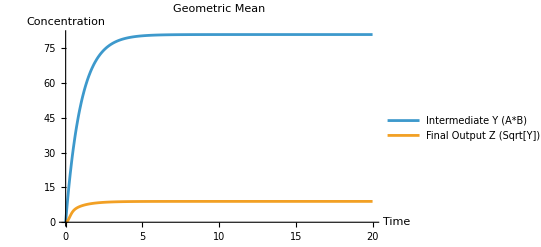

```mathematica
(*Inputs:a=9,b=9. Expected output Z=Sqrt[36]=6*)inputs={conc[A,9],conc[B,9]};
tmax=20;
(*Run simulation*)
sol=SimulateRxnsys[Join[systematicCRN,inputs],tmax];
(*Plot the results*)
Plot[Evaluate[{Y[t],Z[t]}/. sol],{t,0,tmax},PlotLegends->{"Intermediate Y (A*B)","Final Output Z (Sqrt[Y])"},AxesLabel->{"Time","Concentration"},PlotRange->All,PlotLabel->"Geometric Mean"]
```

Stability: These catalytic modules are designed to reach a stable steady state as since the inputs are held constant, and there are annihilation reactions present to prevent explosive dynamics.
Hidden Species: There are no “hidden” species going to infinity here because all species have degradation paths (like Y→∅) or consuming reactions (like 2Z→Z).
Convergence Time: The time to reach steady state is determined by the slowest rate constant.

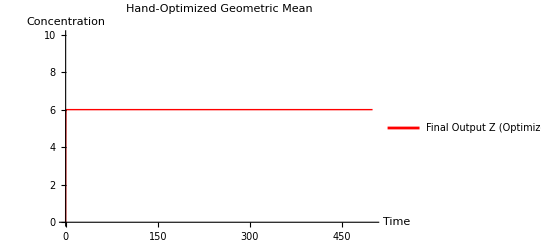

```mathematica
(*Optimized CRN:Removes intermediate Y*)
optimizedCRN={rxn[A+B,A+B+Z,1],rxn[2 Z,Z,1]};
(*Simulate optimized version*)
solOpt=SimulateRxnsys[Join[optimizedCRN,inputs],tmax];
(*Plot optimized result*)
Plot[Evaluate[Z[t]/. solOpt],{t,0,500},PlotStyle->{Directive[Thick,Red]},PlotLegends->{"Final Output Z (Optimized)"},AxesLabel->{"Time","Concentration"},PlotLabel->"Hand-Optimized Geometric Mean",PlotRange->{0,10}]
```

## Part 2: Systematic construction of a CRN with chaotic dynamics (30 points)

You will be constructing a dual-rail bulk CRN that simulates the Rossler attractor.  There are two approaches you could use: (1) construct the CRN by hand, following the principles discussed in class, or if you really want to challenge yourself, (2) write Mathematica code that symbolically analyzes a set of polynomial ODEs and automatically builds the necessary CRN reactions for any dynamical system.  Full credit for approach (1), extra karma points (doesn’t affect your grade) for those who want to do (2).

Your first task is to construct a chemical reaction network that closely approximates the chaotic Rössler attractor:                                                
	           dx/dt=-z-y 
	           dy/dt=x+a y
	           dz/dt=b+z (x-c)
for the parameters a=b=0.2 and c=5.7.  Using a “dual rail” representation for analog values, your CRN should have formal species X_+, X_-, Y_+, Y_-, Z_+, and Z_- that collectively have the desired dynamics, i.e. x(t)=[X_+](t)-[X_-](t), etc.  For starters, you will have the reactions
		X_++X_-⟶^k_fast ∅
		Y_++Y_-⟶^k_fast ∅
		Y_++Y_-⟶^k_fast ∅
Then you will add reactions that ensure that each term of the Rössler ODEs is effectively implemented.  Explain clearly how and why each step works.

In addition to making an analytic argument for the correctness of your CRN, you should directly illustrate and confirm its behavior using numerical simulations. Specifically, you should numerically simulate both the Rössler equations as given and the full mass action ODE’s for your CRN that is designed to implement the Rössler dynamics.

A solid presentation would explain why these are the reactions we need and why they are correct for doing the job.  In addition to making an analytic argument for the correctness of your CRN, a healthy self-skeptic would directly illustrate and confirm the CRN’s behavior using numerical simulations -- for example numerically simulating both the Rössler equations as given and the full mass-action ODEs for your CRN that is designed to implement the Rössler dynamics, and understand how different aspects of the solution depend upon the rate parameters, such as k_fast.

Plot x vs t as well as a parametric plot of (x(t), y(t), z(t)) for both systems.  Also, to illustrate the nature of the representation, plot [X_+] and [X_-] vs t. Describe how these plots depend on k_fast.

The usual caveats apply to this homework -- if you want to change it up to make it more interesting (as opposed to just easier) we welcome that.  If you think there are other ways to tell a compelling story about how your constructions works, rather than the specific tasks  and plots we suggest, please do it the way that feels right to you.   The main point is that a reader shouldn’t have big question marks in their head when they read your work, and also that you shouldn’t belabor points if you just go on and on to cover all bases.  Keep it short and to the point!  Maybe we’ll start taking off points for people who do too much...

```mathematica
RosslerCRN={
(*dx/dt reactions*)
(*The first reaction represents the conversion nof Z into X, using the dual rail implementation requires splitting Z into Zp-Zm to produce Xp-Xm...However due to the negative sign infront of Z, the dual rail system for Z is effectively Zm-Zp this means Zm effectively produces Xp and Zp effectively produces Xm, this is the same logic for the rxn module for Y as well*)
rxn[Zp,Xm,1],rxn[Zm,Xp,1],
rxn[Yp,Xm,1],rxn[Ym,Xp,1],
(*dy/dt reactions*)
(*For these sets of reactions, X combines with Y at rate 1 to form 2 molecules of Y as shown in the ODE, and Y combines with X at rate a to form 2 molecules of Y, these are represented as shown in the rxn modules*)
rxn[Xp,Xp+Yp,1],rxn[Xm,Xm+Ym,1],
rxn[Yp,2Yp,a],rxn[Ym,2Ym,a],
(*dz/dt reactions*)
(*For these set of reactions, in the first reaction modeule we have the initial condition at t=0, where there is a fixed concentration of Zp = b, in the second module, combining Z and X produce *)
rxn[0,Zp,b],
rxn[Zp+Xp,2Zp+Xp,1],rxn[Zm+Xm,Zp+Xm+Zm,1],
rxn[Zp+Xm,Zm+Xm+Zp,1],rxn[Zm+Xp,2Zm+Xp,1],
rxn[Zp,Zm,c],
(* annihilation reactions, as shown in the lecture notes this prevents an infinite blowup in the production species*)
rxn[Xp+Xm,0,kfast],rxn[Yp+Ym,0,kfast],rxn[Zp+Zm,0,kfast]
}/.{a->0.2,b->0.2,c->5.7,kfast->100}
```

{  Zp⟶^1Xm,  Zm⟶^1Xp,  Yp⟶^1Xm,  Ym⟶^1Xp,  Xp⟶^1Xp+Yp,  Xm⟶^1Xm+Ym,  Yp⟶^0.22 Yp,  Ym⟶^0.22 Ym,  0⟶^0.2Zp,  Xp+Zp⟶^1Xp+2 Zp,  Xm+Zm⟶^1Xm+Zm+Zp,  Xm+Zp⟶^1Xm+Zm+Zp,  Xp+Zm⟶^1Xp+2 Zm,  Zp⟶^5.7Zm,  Xm+Xp⟶^1000,  Ym+Yp⟶^1000,  Zm+Zp⟶^1000}

```mathematica
{ " "Yp+Zp⟶^12 Xp, " "Ym+Zm⟶^12 Xm, " "0⟶^12 Xp, " "0⟶^12 Xm, " "Xp⟶^1Xp+Yp, " "Xm⟶^1Xm+Yp, " "Yp⟶^0.22 Yp, " "Ym⟶^0.22 Ym, " "0⟶^0.2Zp, " "0⟶^0.2Zm, " "Xp+Zp⟶^1Xp+2 Zp, " "Xm+Zm⟶^1Xm+2 Zp, " "Xm+Zp⟶^1Xp+2 Zm, " "Xp+Zm⟶^1Xm+2 Zm, " "Zp⟶^5.72 Zp,m, " "Xm+Xp⟶^1000, " "Ym+Yp⟶^1000, " "Zm+Zp⟶^1000}
```

{  Yp+Zp⟶^12 Xp,  Ym+Zm⟶^12 Xm,  0⟶^12 Xp,  0⟶^12 Xm,  Xp⟶^1Xp+Yp,  Xm⟶^1Xm+Yp,  Yp⟶^0.22 Yp,  Ym⟶^0.22 Ym,  0⟶^0.2Zp,  0⟶^0.2Zm,  Xp+Zp⟶^1Xp+2 Zp,  Xm+Zm⟶^1Xm+2 Zp,  Xm+Zp⟶^1Xp+2 Zm,  Xp+Zm⟶^1Xm+2 Zm,  Zp⟶^5.72 Zp,m,  Xm+Xp⟶^1000,  Ym+Yp⟶^1000,  Zm+Zp⟶^1000}

```mathematica
RxnsysToOdesys[RosslerCRN]
(*mass action ODEs for this system*)
```

{Xm[0]==0,Xp[0]==0,Ym[0]==0,Yp[0]==0,Zm[0]==0,Zp[0]==0,Xm'[t]==0.-100 Xm[t] Xp[t]+Yp[t]+Zp[t],Xp'[t]==0.-100 Xm[t] Xp[t]+Ym[t]+Zm[t],Ym'[t]==0.+Xm[t]-0.8 Ym[t]-100 Ym[t] Yp[t],Yp'[t]==0.+Xp[t]-0.8 Yp[t]-100 Ym[t] Yp[t],Zm'[t]==0.-Zm[t]+Xp[t] Zm[t]+5.7 Zp[t]+Xm[t] Zp[t]-100 Zm[t] Zp[t],Zp'[t]==0.2+Xm[t] Zm[t]-6.7 Zp[t]+Xp[t] Zp[t]-100 Zm[t] Zp[t]}

```mathematica
tmax=40;sol=SimulateRxnsys[RosslerCRN~Join~{conc[Xp,1],conc[Yp,1],conc[Zp,1],conc[Xm,0],conc[Ym,0],conc[Zm,0]},tmax];
```

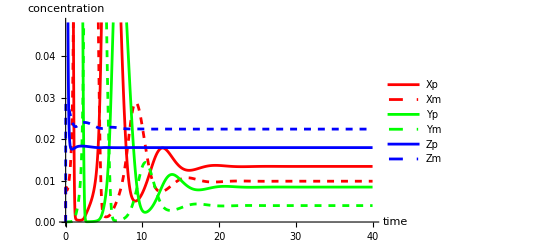

```mathematica
Plot[Evaluate[{Xp[t],Xm[t],Yp[t],Ym[t],Zp[t],Zm[t]}/.sol],{t,0,tmax},PlotStyle->{{Red},{Dashed,Red},{Green},{Dashed,Green},{Blue},{Dashed,Blue}},AxesLabel->{"time","concentration"},PlotLegends->{Xp,Xm,Yp,Ym,Zp,Zm}]
```

```mathematica
ParametricPlot3D[Evaluate[{Xp[t]-Xm[t],Yp[t]-Ym[t],Zp[t]-Zm[t]}/.sol],{t,0,tmax},AxesLabel->{x,y,z},ColorFunction->Function[{x,y,z,t},Hue[t]]]
```

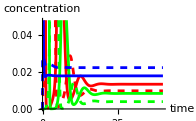
To determine dependence on kfast, we plot again with different kfast values.
Increasing kfast appears to both decrease the amplitude of initial oscillations in the trajectory plot as well as shrink the bounds of z in the parameterization plot. Below i show the plots for kfast values of 10,30,60, and 200
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

## Part 3: Engage the material (30 points)

As usual, this is place where you assign yourself an exercise and work through it to understand something uniquely of interest to you.  Thus is it kind of against the intentions if you just take one of our sample questions below and try to address it.  We want you to be asking your own question, and the sample questions are primarily there to serve as examples of the kinds of things that might be natural to ask... but there are an infinity of things to ask, so you ought to be able to come up with something equally interesting.  In fact, you ought to be coming up with at least one question every minute while you listen to a lecture or read the class notes or Mathematica notebooks.  They are all valid, so long as you engage with them to the depth that roughly matches the Part 1 and Part 2 questions... and that your questions relate to the material and concepts of this class, rather than some other class.   

You can think of your work here as being spiritually aligned a humanities essay, intended to challenge you to engage with the material and find your own meaning and understanding of it.    The only hard requirements are that, regardless of what question you eventually tackle, you go through everything in DeterministicCRNsInBulk.nb and DynamicalSystems.nb and contemplate it before you decide what you will do for the homework.   Read the article first; then write your essay about it.  So to speak. 

Note that although the notebooks explicitly present a number of sometimes very concrete questions, we don’t particularly want you to do anything that we suggested.  You can take these questions as example meant to stimulate your imagination.   You can work on these questions if that’s what you want, but we think you’ll get much more out of it if you pose your own.

Asking questions, allowing yourself to be curious, testing your knowledge in both simple and challenging cases... but especially, asking your own questions as a way to actively ground your understanding... is of such great importance that I really hope you’ll work hard to practice asking and following up on your ask.

A good “essay” will clearly state a question and why you are interested in it, see how far you can go toward answering it, assess how rigorous your answer is in terms of whether there are exceptions, caveats, approximations, preconditions, etc., and comment on what it means to you.   A really good “essay” will have a punchline; it will convince the reader of something.  A good “effort” will perhaps have less clear of a question or questions, but will help you understand the material by testing and trying things, even if it might not be so interesting to anyone else -- and that’s OK too.  Often the best questions are the simplest, the ones you think “nobody will be impressed if I understand that” -- but where understanding it well is actually the most valuable thing you can do.

In your write-up, clearly state your question related to programming computation and/or dynamics in CRNs, see how far you can go toward answering it, and assess how rigorous your answer is in terms of whether there are exceptions, caveats, approximations, preconditions, etc.

Bottom line: as with previous homework assignments, we are encouraging you to go in whatever directions compel or inspire you.  And we hope that will not be just copy-pasting one of the sample questions we posed in the notebooks!

Enjoy!

Here are some sample questions about analog catalytic stead-state computation by CRNs.  These are too large-scale for most students, so don’t that that as the template here -- we recommend asking simpler, more concrete questions. 

Can any algebraic expression that has positive output for all positive input values be written in a form such that all subexpressions are always positive?

Can any algebraic expression be implemented by CRNs that use reactions with at most two reactants and at most two products?

For a different I/O convention where a real-valued variable is represented by the logarithm of its concentration, what analog function modules can we implement?

For a different I/O convention where all species concentrations must remain less than 1 at all times (e.g. they can’t diverge to infinity) how does this restrict what can be implemented?

For a different I/O convention where all non-input species always start at zero, rather than starting at arbitrary concentrations, how does this change what can or cannot be implemented?

Here are some sample questions about about programming dynamical behavior in CRNs.  Ditto as above.

Can the dual-rail polynomial ODE construction be used to design CRNs for steady-state analog computation of algebraic expressions?  And if so, how does it compare (e.g. in terms of number of species and reactions, or time to compute, or other metrics) to the previously presented constructions?  Does it generalize to algebraic expressions that have both positive and negative inputs, outputs, and subexpressions?
	
Can the dual-rail polynomial ODE construction be generalized to systems of non-polynomial ODEs, e.g. via ratios of polynomials, algebraic expressions, or through Taylor expansions or other approximations, or other exact methods?  Can you work thought a specific chosen example?  Can you assess in general when it will or will not work?  
	
For polynomial ODEs that just so happen to involve variables than never go negative, is it possible to derive a simpler construction that uses single-rail variables?
	
For polynomial ODEs that have higher-order terms, e.g. x^7, the standard dual-rail construction will require a high-order reaction, e.g. 7 X →7X+Y, that might seem difficult to directly implement.  Can such reactions be indirectly implemented using a set of several bimolecular reactions?

Dynamics in stochastic CRNS.
In the cell nuclues, CRNs are much more dynamic than can be represented by most analog CRNs. The Rössler system is a benchmark for deterministic chaos, characterized by extreme sensitivity to initial conditions and parameters. In a cell nucleus, however, we do not have a “well-mixed beaker.” By introducing macromolecular crowding (MMC) through trapping and nonconstant reaction rates, we are asking whether biological “messiness” acts as a functional “buffer” that preserves complex dynamics in the face of environmental noise.
 in this approach, I use an implementation of the linear solvation energy relationship which is described in assumptions to program a CRN which is representative of an approximation to the stochastic dynamics presented by the effects of macromolecular crowding within the nucleus. 
Assumptions
CRN dynamics in the cell nucleus is not recapitulated in a well mixed CRN model.
	This is due to the effects of exclusion volume which follows from macromolecular crowding. In the nucleus, the presence of large molecules can cause strong and weak 		effects, weak effects likely from transient hydrophobic interactions and Van Der Waal forces. Strong effects are due to mechanisms that tend to kinetically trap molecules such 		that they are unable to participate in reactions, this may or may not be correlated to their 	decay mechanisms. In my simulation it is assumed that these are independent events 		since trapped molecules can eventually get freed.  While this does not violate mass-action kinetics, it introduces resonance/damping into the system depending on whether 		the macromolecular effects are cooperatively synergetic or not		
Macromolecular crowding effects can be recapitulated via the use of the linear solvation energy relationship as developed by Kamlet and Taft (Droplets of Life). This is a three parameter polarity scale inclusive of the scales of hydrogen bond donor acidity, hydrogen bond acceptor basicity, and the polarizability of the molecule. In my system, the rate constant is the solute property used in this relationship. The effective rate constant in our case is given by 
	K = K_0 + s*pi + a*alpha + b*beta
	Where s, a and b are solute dependent coefficients and pi, alpha, beta represent the hydrogen bond donor acidity, hydrogen bond 		acceptor basicity, and the polarizability of the molecule respectively.
	s*pi + a*alpha + b*beta is assumed in my model to be linearly dependent on K_0 to test the proof of concept since no specific 			molecules are implied. In this approach, s*pi + a*alpha + b*beta = 1/2(K_0). To simulate the stochastic nature, 1/2(K_0) is drawn from a 	Poisson distribution with mean 1/2(K_0). Initially, this was done using K_0 + s*pi + a*alpha + b*beta, but this lead to significant divergence of our system from the ideal solution.
Construction of model:
The “Memory” Effect: By adding the X,Y,Z->Xtrapped​, Ytrapped​, Ztrapped​ reactions, our initial ODE system is now a Delay Differential Equation (DDE) approximation. In a standard CRN, the “now” only depends on the “now.” In this MMC-CRN, the “trapped” species act as a reservoir for future reactions effectively prolonging the reaction, and a “rate limiting” mechanism.
The Poisson Logic: Using Clip[PoissonDistribution[0.5], {-0.5, 0.5}] creates a binary switching rate. Your rate constant is either K0-0.5, K0​, K0​+0.5 or somewhere in between. This represents a “micro-environment” model where a molecule is either in a “crowded” pocket or a “free” pocket, rather than a smooth Gaussian average.

```mathematica
RosslerCRNMMC={
(*dx/dt reactions*)
(*Clip sets the bounds of the Poisson Distribution*)
rxn[Zcp,Xcm,1+Clip[RandomVariate[PoissonDistribution[0.5]],{-0.5,0.5}]],
rxn[Zcm,Xcp,1+Clip[RandomVariate[PoissonDistribution[0.5]],{-0.5,0.5}]],
rxn[Ycp,Xcm,1+Clip[RandomVariate[PoissonDistribution[0.5]],{-0.5,0.5}]],
rxn[Ycm,Xcp,1+Clip[RandomVariate[PoissonDistribution[0.5]],{-0.5,0.5}]],


(*Ztcm, Ytcm, and Xtcm are introduced to represent the kinetically trapped states of Zcm, Xcm, and Ycm, this is a reversible transition with transitioning from the trapped state to a free state more favorable in this model*)
rxn[Zcm,Ztcm,0.5+Clip[RandomVariate[PoissonDistribution[0.25]],{-0.25,0.25}]],
rxn[Ztcm,Zcm,1.2+Clip[RandomVariate[PoissonDistribution[0.6]],{-0.6,0.6}]],
rxn[Zcp,Ztcp,0.5+Clip[RandomVariate[PoissonDistribution[0.25]],{-0.25,0.25}]],rxn[Ztcp,Zcp,1.2+Clip[RandomVariate[PoissonDistribution[0.6]],{-0.6,0.6}]],

rxn[Ycm,Ytcm,0.5+Clip[RandomVariate[PoissonDistribution[0.25]],{-0.25,0.25}]],
rxn[Ytcm,Ycm,1.8+Clip[RandomVariate[PoissonDistribution[0.9]],{-0.9,0.9}]],
rxn[Ycp,Ytcp,0.5+Clip[RandomVariate[PoissonDistribution[0.25]],{-0.25,0.25}]],rxn[Ytcp,Ycp,0.8+Clip[RandomVariate[PoissonDistribution[0.4]],{-0.4,0.4}]],

rxn[Xcm,Xtcm,1.4+Clip[RandomVariate[PoissonDistribution[0.7]],{-0.7,0.7}]],
rxn[Xtcm,Xcm,3+Clip[RandomVariate[PoissonDistribution[1.5]],{-1.5,1.5}]],
rxn[Xcp,Xtcp,1.8+Clip[RandomVariate[PoissonDistribution[0.9]],{-0.9,0.9}]],
rxn[Xtcp,Xcp,3+Clip[RandomVariate[PoissonDistribution[1.5]],{-1.5,1.5}]],

(*dy/dt reactions*)
rxn[Xcp,Xcp+Ycp,1+Clip[RandomVariate[PoissonDistribution[0.5]],{-0.5,0.5}]],
rxn[Xcm,Xcm+Ycm,1+Clip[RandomVariate[PoissonDistribution[0.5]],{-0.5,0.5}]],
rxn[Ycp,2Ycp,0.2+Clip[RandomVariate[PoissonDistribution[0.1]],{-0.1,0.1}]],
rxn[Ycm,2Ycm,0.2+Clip[RandomVariate[PoissonDistribution[0.1]],{-0.1,0.1}]],


(*dz/dt reactions*)
rxn[0,Zcp,0.2+Clip[RandomVariate[PoissonDistribution[0.1]],{-0.1,0.1}]],
rxn[Zcp+Xcp,2Zcp+Xcp,0.2+Clip[RandomVariate[PoissonDistribution[0.1]],{-0.1,0.1}]],
rxn[Zcm+Xcm,Zcp+Xcm+Zcm,1+Clip[RandomVariate[PoissonDistribution[0.5]],{-0.5,0.5}]],
rxn[Zcp+Xcm,Zcm+Xcm+Zcp,1+Clip[RandomVariate[PoissonDistribution[0.5]],{-0.5,0.5}]],
rxn[Zcm+Xcp,2Zcm+Xcp,1+Clip[RandomVariate[PoissonDistribution[0.5]],{-0.5,0.5}]],
rxn[Zcp,Zcm,5.7+Clip[RandomVariate[PoissonDistribution[3.85]],{-3.85,3.85}]],



(* annihilation reactions *)
rxn[Xcp+Xcm,0,kfast],rxn[Ycp+Ycm,0,kfast],rxn[Zcp+Zcm,0,kfast]
}/.{a->0.2,b->0.2,c->5.7,kfast->200}
```

{  Zcp⟶^1Xcm,  Zcm⟶^1Xcp,  Ycp⟶^1.5Xcm,  Ycm⟶^1Xcp,  Zcm⟶^0.5Ztcm,  Ztcm⟶^1.8Zcm,  Zcp⟶^0.5Ztcp,  Ztcp⟶^1.2Zcp,  Ycm⟶^0.75Ytcm,  Ytcm⟶^1.8Ycm,  Ycp⟶^0.5Ytcp,  Ytcp⟶^0.8Ycp,  Xcm⟶^2.1Xtcm,  Xtcm⟶^4Xcm,  Xcp⟶^2.7Xtcp,  Xtcp⟶^4.5Xcp,  Xcp⟶^1.5Xcp+Ycp,  Xcm⟶^1.5Xcm+Ycm,  Ycp⟶^0.22 Ycp,  Ycm⟶^0.22 Ycm,  0⟶^0.2Zcp,  Xcp+Zcp⟶^0.2Xcp+2 Zcp,  Xcm+Zcm⟶^1Xcm+Zcm+Zcp,  Xcm+Zcp⟶^1.5Xcm+Zcm+Zcp,  Xcp+Zcm⟶^1.5Xcp+2 Zcm,  Zcp⟶^9.55Zcm,  Xcm+Xcp⟶^2000,  Ycm+Ycp⟶^2000,  Zcm+Zcp⟶^2000}

```mathematica
tmax=40;sol=SimulateRxnsys[RosslerCRNMMC~Join~{conc[Xcp,1],conc[Ycp,1],conc[Zcp,1],conc[Xcm,0],conc[Ycm,0],conc[Zcm,0]},tmax];
```

```mathematica
{Xcm,Xcp,Xtcm,Xtcp,Ycm,Ycp,Ytcm,Ytcp,Zcm,Zcp,Ztcm,Ztcp}/.%65
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

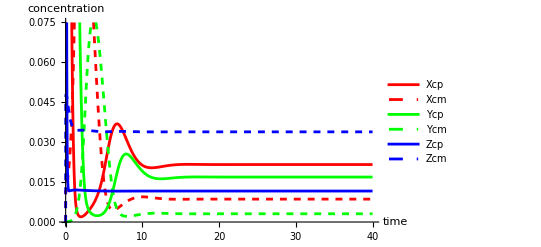

```mathematica
Plot[Evaluate[{Xcp[t],Xcm[t],Ycp[t],Ycm[t],Zcp[t],Zcm[t]}/.sol],{t,0,tmax},PlotStyle->{{Red},{Dashed,Red},{Green},{Dashed,Green},{Blue},{Dashed,Blue}},AxesLabel->{"time","concentration"},PlotLegends->{Xcp,Xcm,Ycp,Ycm,Zcp,Zcm}]
```

```mathematica
ParametricPlot3D[Evaluate[{Xcp[t]-Xcm[t],Ycp[t]-Ycm[t],Zcp[t]-Zcm[t]}/.sol],{t,0,tmax},AxesLabel->{x,y,z},ColorFunction->Function[{x,y,z,t},Hue[t]]]
```

-Graphics3D-

```mathematica
RxnsysToOdesys[RosslerCRN]
```

{Xcm[0]==0,Xcp[0]==0,Xtcm[0]==0,Xtcp[0]==0,Ycm[0]==0,Ycp[0]==0,Ytcm[0]==0,Ytcp[0]==0,Zcm[0]==0,Zcp[0]==0,Ztcm[0]==0,Ztcp[0]==0,Xcm'[t]==0.-2.1 Xcm[t]-100 Xcm[t] Xcp[t]+4 Xtcm[t]+1.5 Ycp[t]+Zcp[t]-1.5 Xcm[t] Zcp[t],Xcp'[t]==0.-2.7 Xcp[t]-100 Xcm[t] Xcp[t]+4.5 Xtcp[t]+1.5 Ycm[t]+Zcm[t]+1.5 Xcm[t] Zcp[t],Xtcm'[t]==0.+2.1 Xcm[t]-4 Xtcm[t],Xtcp'[t]==0.+2.7 Xcp[t]-4.5 Xtcp[t],Ycm'[t]==0.+Xcm[t]-1.8 Ycm[t]-100 Ycm[t] Ycp[t]+2.7 Ytcm[t],Ycp'[t]==0.+Xcp[t]-1.7 Ycp[t]-100 Ycm[t] Ycp[t]+0.8 Ytcp[t],Ytcm'[t]==0.+0.5 Ycm[t]-2.7 Ytcm[t],Ytcp'[t]==0.+0.5 Ycp[t]-0.8 Ytcp[t],Zcm'[t]==0.-1.75 Zcm[t]+Xcp[t] Zcm[t]+9.55 Zcp[t]+1.5 Xcm[t] Zcp[t]-100 Zcm[t] Zcp[t]+1.2 Ztcm[t],Zcp'[t]==0.2+Xcm[t] Zcm[t]-11.05 Zcp[t]+0.2 Xcp[t] Zcp[t]-100 Zcm[t] Zcp[t]+1.2 Ztcp[t],Ztcm'[t]==0.+0.75 Zcm[t]-1.2 Ztcm[t],Ztcp'[t]==0.+0.5 Zcp[t]-1.2 Ztcp[t]}

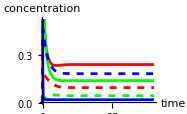
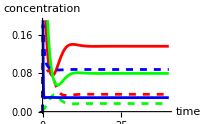
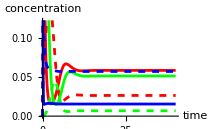
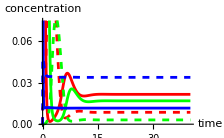
Using the same kfast variations as in problem 2 (10,30,60,200) this system appears to have less oscillations as compared to our previous model, and in general appears to have amplitudes that are inversely correlated with the kfast level as we saw previously but with a slight dip, from right to left we see a decrease in the amplitude of the concentrations, as kfast increases.
-Graphics--Graphics--Graphics--Graphics-